# Alguns Exemplos do Mathematica

O objetivo da célula da texto é incluir informações úteis para a utilização do arquivo...

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos

[] -- para função
() -- para agrupar
{} -- para listas

```mathematica
data={{1,1},{5,2},{10,4},{15,8},{20,16},{25,32},{30,64},{35,128},{42, 128 10}, {49, 128 10 10},{56, 120 10 10 10}};
model =  x^n;
```

```mathematica
FindFit[data, model, x,n]
```

```mathematica
x/.{x->1.2316687191855076}
```

1.23167

```mathematica
exp=x/.FindFit[data, model, x,n]
```

1.23167

```mathematica
fit[x_]:=exp^x
```

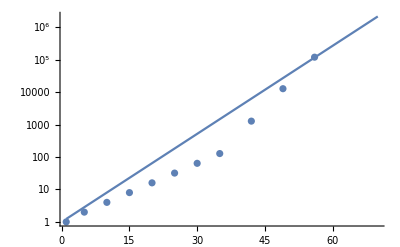

```mathematica
o1=ListLogPlot[data];
o2=LogPlot[fit[x],{x,1,70}];
Show[{o1,o2}, PlotRange-> All]
```

```mathematica
(* impedancia interna de condutor sem alma de aco *)
(* impedancia interna de condutores cilindricos *) 
(*Mur=90 para cables de aco*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:90, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
Zin[2 π 6000., 10^-7, 0.01]
```

0.00742869+0.00734781 ⅈ

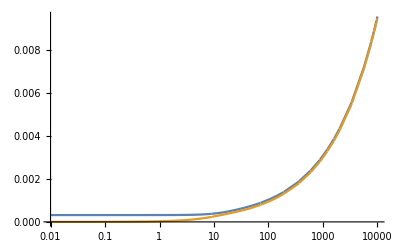

```mathematica
LogLinearPlot[{
Re[Zin[2 π x, 10^-7, 0.01]],Im[Zin[2 π x, 10^-7, 0.01]]},{x, 0.01, 10000}]
```

```mathematica
(* rotinas para copiar o linspace e o logspace do matlab *)
logspac = Compile[{{i,_Real},{f,_Real},{np,_Integer}},
                 Table[10.0^(i + (x*(f - i))/(Floor[np] - 1)), {x, 0, np - 1}]
                 ];
```

```mathematica
linspac = Compile[{{i,_Real}, {f,_Real}, {np,_Integer}}, 
                 Table[i + (x*(f - i))/(Floor[np] - 1), {x, 0, np - 1}]];
```

```mathematica
freq=logspac[-2, 6, 200];
```

```mathematica
imp = Zin[2 π freq, 10^-7, 0.01];
```

```mathematica
Length[imp]
```

200

```mathematica
fun[x_,a_:10]:= a x^2
```

```mathematica
fun[2]
```

40

```mathematica
TeXForm[Integrate[f[x,a],x]]
```

\int f(x,a) \, dx

```mathematica
fun@{2, 1}
```

{40,10}

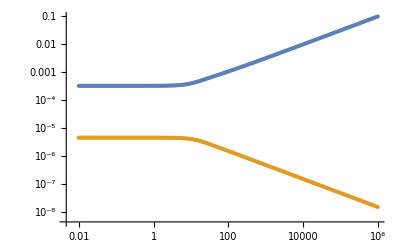

```mathematica
ListLogLogPlot[{Transpose[{freq,Re[imp]}],
Transpose@{freq,Im[imp]/(2 π freq)}}]
```